The EKG Sensor measures cardiac electrical potential waveforms (voltages produced during the contraction of the heart). It can be used to make standard 3-lead EKG tracings to record electrical activity in the heart, or to collect surface EMG recordings to study contractions in muscles in your arm, leg or jaw.

Connect the sensor to your computer, then evaluate the following input (need help on evaluating inputs?):

```mathematica
sensor=DeviceOpen["Vernier"]
```

StringJoin::string: String expected at position 2 in Connected (<>Missing[KeyAbsent,15]<>).

StringJoin::string: String expected at position 2 in Not Connected (<>Missing[KeyAbsent,15]<>).

DeviceObject[…]

If the “Status” field in the output shows a green dot, you are successfully connected to the sensor.

If the "Status" shows a yellow dot or a red dot, then click here to open the Troubleshooting Guide.

You can now read from the sensor:

```mathematica
DeviceRead[sensor]
```

0.90065

You can also read the most recent values recorded in the sensor’s buffer:

```mathematica
DeviceReadBuffer[sensor]
```

StructuredArray[QuantityArray, {540}, <Kilopascals>]

Or take measurements over a given time interval. In the input below we are measuring every 0.1 second for a total duration of 10 seconds. A progress bar is shown while the Wolfram Language is reading data:

```mathematica
data=DeviceReadTimeSeries[sensor,{10,0.05}]
```

TimeSeries[…]

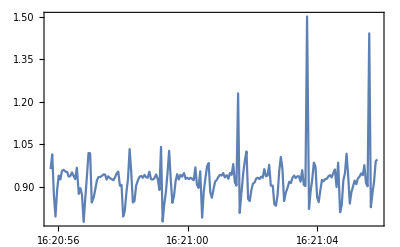

```mathematica
DateListPlot[data,PlotRange->All]
```

When you are done, you can close the connection to the sensor:

```mathematica
DeviceClose[sensor]
```

After you close the connection you can unplug the USB cable and connect another sensor.